```mathematica
f0=0.1234
```

0.1234

```mathematica
fx0=0.9876
```

0.9876

```mathematica
fxx0=0.1
```

0.1

```mathematica
f1=0.5678
```

0.5678

```mathematica
fx1=-0.1111
```

-0.1111

```mathematica
fxx1=-0.1
```

-0.1

```mathematica
c0=f0
```

0.1234

```mathematica
c1=5*f0+fx0
```

1.6046

```mathematica
c2=10*f0+4*fx0+fxx0/2
```

5.2344

```mathematica
c5=f1
```

0.5678

```mathematica
c4=5*f1-fx1
```

2.9501

```mathematica
c3=10*f1-4*fx1+fxx1/2
```

6.0724

```mathematica
g=c0*(1-x)^5+c1*x*(1-x)^4+c2*x^2*(1-x)^3+c3*x^3*(1-x)^2+c4*x^4*(1-x)+c5*x^5
```

0.1234 (1-x)^5+1.6046 (1-x)^4 x+5.2344 (1-x)^3 x^2+6.0724 (1-x)^2 x^3+2.9501 (1-x) x^4+0.5678 x^5

```mathematica
gx=D[g,x]
```

0.9876 (1-x)^4+4.0504 (1-x)^3 x+2.514 (1-x)^2 x^2-0.3444 (1-x) x^3-0.1111 x^4

```mathematica
gxx=D[gx,x]
```

0.1 (1-x)^3-7.1232 (1-x)^2 x-6.0612 (1-x) x^2-0.1 x^3

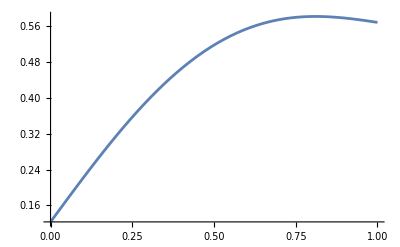

```mathematica
Plot[g,{x,0,1}]
```

```mathematica
points=Import["C:\\Users\\deber\\GeometricTools\\GTL\\UnitTests\\Mathematics\\Interpolation\\1D\\HermiteQuintic1Order0Single.txt","CSV"];
```

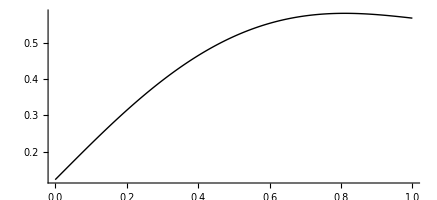

```mathematica
Graphics[Line[points],Axes->True,AspectRatio->Full]
```

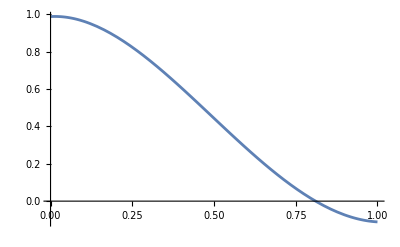

```mathematica
Plot[gx,{x,0,1}]
```

```mathematica
points=Import["C:\\Users\\deber\\GeometricTools\\GTL\\UnitTests\\Mathematics\\Interpolation\\1D\\HermiteQuintic1OrderXSingle.txt","CSV"];
```

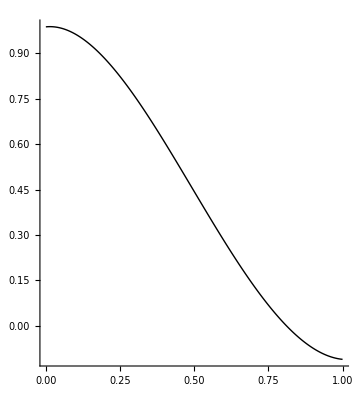

```mathematica
Graphics[Line[points],Axes->True,AspectRatio->Full]
```

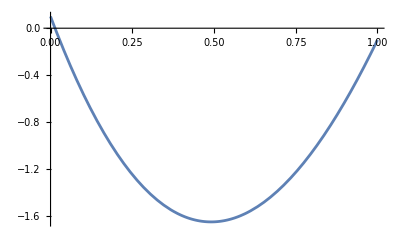

```mathematica
Plot[gxx,{x,0,1}]
```

```mathematica
points=Import["C:\\Users\\deber\\GeometricTools\\GTL\\UnitTests\\Mathematics\\Interpolation\\1D\\HermiteQuintic1OrderXXSingle.txt","CSV"];
```

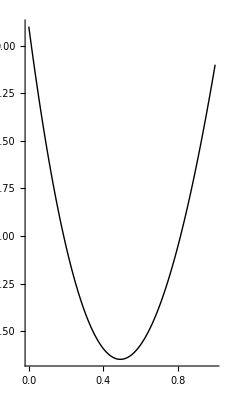

```mathematica
Graphics[Line[points],Axes->True,AspectRatio->Full]
```